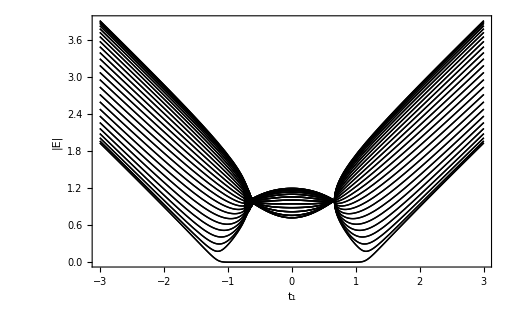

```mathematica
num=50;
t2=1;
g=4/3;
H=Table[0,{i,1,num},{j,1,num}];
For[i=1,i<num,i=i+2,H[[i,i+1]]=t1+g/2];
For[i=1,i<num,i=i+2,H[[i+1,i]]=t1-g/2];
For[i=2,i<num,i=i+2,H[[i,i+1]]=t2];
For[i=2,i<num,i=i+2,H[[i+1,i]]=t2];
eigfun[t1_]:=Sort[Abs[Eigenvalues[H]]];
picSSH=Plot[eigfun[t1],{t1,-3,3},PlotStyle->{Black,Thin},Axes->False,Frame->True,FrameLabel->{{RawBoxes[RowBox[{"|","E","|"}]],None},{HoldForm[Subscript[t, 1]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

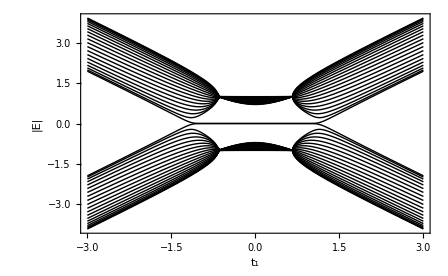

```mathematica
num=40;
t2=1;
g=4/3;
H=Table[0,{i,1,num},{j,1,num}];
For[i=1,i<num,i=i+2,H[[i,i+1]]=t1+g/2];
For[i=1,i<num,i=i+2,H[[i+1,i]]=t1-g/2];
For[i=2,i<num,i=i+2,H[[i,i+1]]=t2];
For[i=2,i<num,i=i+2,H[[i+1,i]]=t2];
eigfun[t1_]:=Sort[Re[Eigenvalues[H]]];
picSSH=Plot[eigfun[t1],{t1,-3,3},PlotStyle->{Black,Thin},Axes->False,Frame->True,FrameLabel->{{RawBoxes[RowBox[{"|","E","|"}]],None},{HoldForm[Subscript[t, 1]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

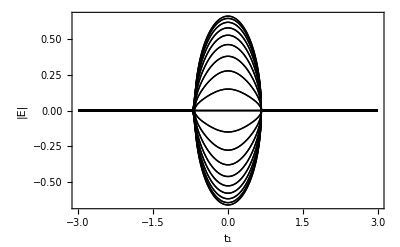

```mathematica
num=40;
t2=1;
g=4/3;
H=Table[0,{i,1,num},{j,1,num}];
For[i=1,i<num,i=i+2,H[[i,i+1]]=t1+g/2];
For[i=1,i<num,i=i+2,H[[i+1,i]]=t1-g/2];
For[i=2,i<num,i=i+2,H[[i,i+1]]=t2];
For[i=2,i<num,i=i+2,H[[i+1,i]]=t2];
eigfun[t1_]:=Sort[Im[Eigenvalues[H]]];
picSSH=Plot[eigfun[t1],{t1,-3,3},PlotStyle->{Black,Thin},Axes->False,Frame->True,FrameLabel->{{RawBoxes[RowBox[{"|","E","|"}]],None},{HoldForm[Subscript[t, 1]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
num=40;
```